```mathematica
Signal=Import["\\\\files.unr.edu\\users\\nvagner\\Downloads\\738.txt","Table"];
Template=Import["\\\\files.unr.edu\\users\\nvagner\\Downloads\\signalTemplate14695-738.out","Table"];
h=-0.067
```

-0.067

```mathematica
Length[Signal]
S2=Signal;
S3=Round[S2];
S4=S3-Min[S3]+1;
```

24

```mathematica
Length[Template]
T2=h*Template;
T3=Round[T2];
T4=T3-Min[S3]+1;
```

24

```mathematica
array1=RandomInteger[{1,5},{24,61}]; (*tile color values*)
array2=RandomInteger[{1,10},{24,61}]; (*edge colors values*)
spacing=0.16
```

0.16

```mathematica
g=Graphics[Table[Style[Rectangle[{i-1+spacing,j-1+spacing},{i,j}],FaceForm[ColorData[97,"ColorList"][[S4[[i,j]]]]],EdgeForm[{Thickness[0.005],ColorData[97,"ColorList"][[T4[[i,j]]]]}]],{i,1,24},{j,1,61} ],PlotRange->{{0,24},{0,61}},AspectRatio->2.54];
```

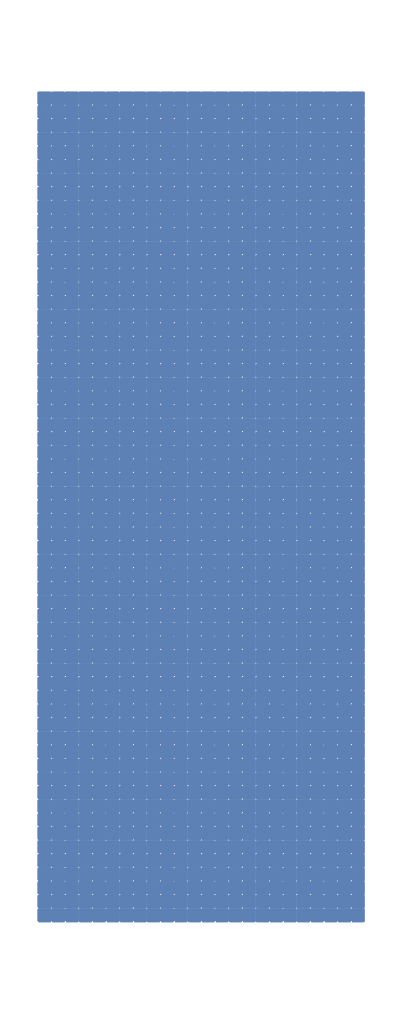

```mathematica
Rotate[g,1.5708]
```

```mathematica
RepresentArrays[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},{rows,cols}=Dimensions[array1];
grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.005],ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]}],ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]],{i,1,rows},{j,1,cols}];
Graphics[grid,PlotRange->{{0,rows},{0,cols}},AspectRatio->2.54]]
```

```mathematica
RepresentArrays2[array1_,array2_,max2_,min2_]:=Module[{rows,cols,grid},{rows,cols}=Dimensions[array1];
grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.005],ColorData["TemperatureMap"][Rescale[array1[[i,j]],{min2,max2}]]}],FaceForm[{Opacity[0.01],ColorData["TemperatureMap"][Rescale[array2[[i,j]],{min2,max2}]]}]],{i,1,rows},{j,1,cols}];
Graphics[grid,PlotRange->{{0,rows},{0,cols}},AspectRatio->2.54]]
```

0.0871

-0.0871

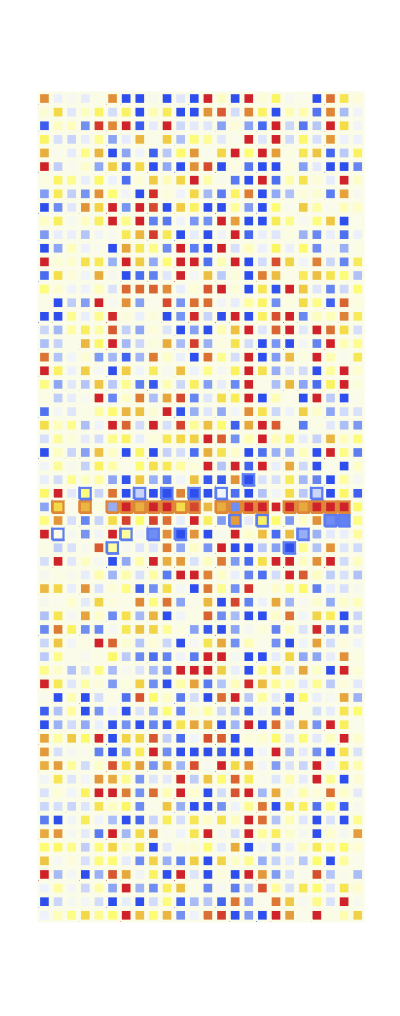

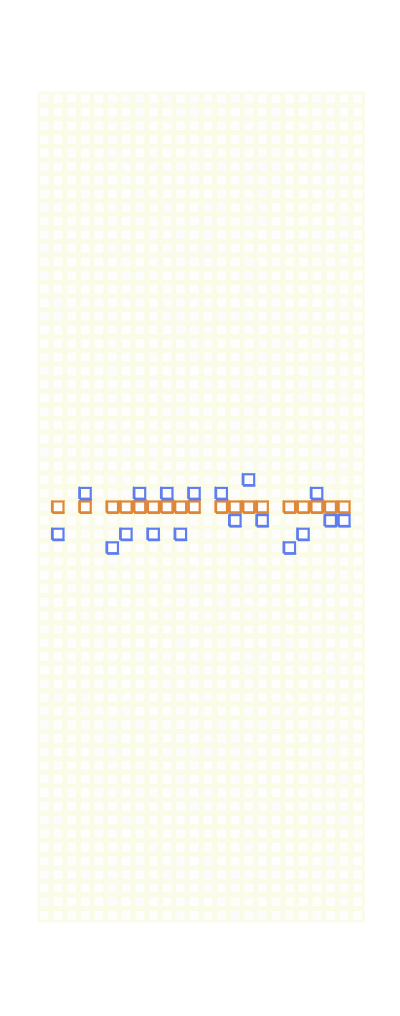

```mathematica
Max2=1.3*Max[Max[T2]]
Min2=1.3*Min[Min[T2]]
g2=RepresentArrays[T2,S2,Max2,Min2];
Rotate[g2,-1.5708]
g3=RepresentArrays2[T2,S2,Max2,Min2];
Rotate[g3,-1.5708]
```